```mathematica
Func[t_,α_,N_]:=(t/α)^(α N)((1-t)/(1-α))^(N-α N)1/Sqrt[2 Pi α(1-α )N]
```

```mathematica
Func2[t_,α_,N_]:=Factorial[N]/(Factorial[α N]Factorial[N-α N])t^(α N)(1-t)^(N-α N)
```

```mathematica
Func3[t_,α_,N_]:=PDF[BinomialDistribution[N,t],α N]
```

```mathematica
Func4[t_,α_,N_]:=PDF[NormalDistribution[N t,Sqrt[N t(1-t)]],α N]
```

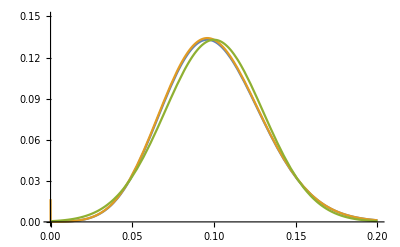

```mathematica
Plot[{Func2[0.1,α,100],Func[0.1,α,100],Func4[0.1,α,100]},{α,0,0.2},PlotRange->{0,0.15}]
```

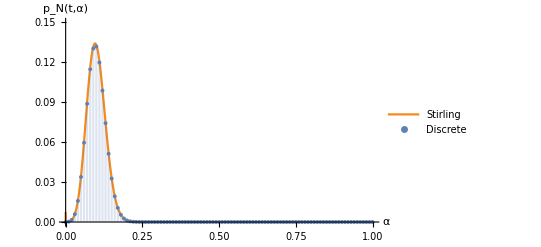

```mathematica
Show[Plot[Func[0.1,α,100],{α,0,1},PlotRange->{0,0.15},AxesLabel->{"α","p_N(t,α)"},PlotStyle->ColorData[106,"ColorList"],PlotLegends->Placed[{"Stirling"},{0.81,0.8}]],DiscretePlot[Func3[0.1,α,100],{α,0,1,0.01},PlotMarkers->{Automatic, Tiny},PlotLegends->Placed[{"Discrete"},{0.835,0.9}]]]
```

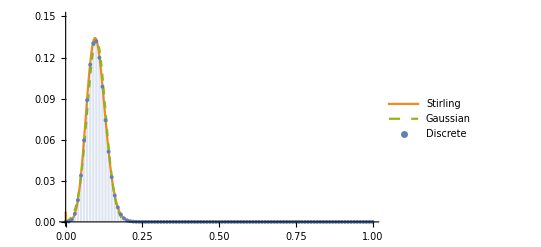

```mathematica
Show[Plot[Func[0.1,α,100],{α,0,1},PlotRange->{0,0.15},PlotStyle->ColorData[106,"ColorList"],PlotLegends->Placed[{"Stirling"},{0.81,0.8}]],Plot[Func4[0.1,α,100],{α,0,1},PlotRange->{0,0.15},AxesLabel->{"α","p_N(t,α)"},PlotStyle->{Dashed,ColorData[102,"ColorList"]},PlotLegends->Placed[{"Gaussian"},{0.8,0.7}]],DiscretePlot[Func3[0.1,α,100],{α,0,1,0.01},PlotRange->{0,0.15},PlotMarkers->{Automatic, Tiny},PlotLegends->Placed[{"Discrete"},{0.835,0.9}]]]
```